#### SiV+cavity data:

```mathematica
names=
Sort[Cases[FileNames[],_?((StringMatchQ[#,"*BF SiV*.txt"])&&!StringMatchQ[#,"*History*"]&)],FileDate[#1,"Modification"]<FileDate[#2,"Modification"]&];
Table[Print[i,": ",names[[i]]],{i,1,Length[names]}];
```

1: BF SiV and cavity after installing interferometer after gas tuning1.txt

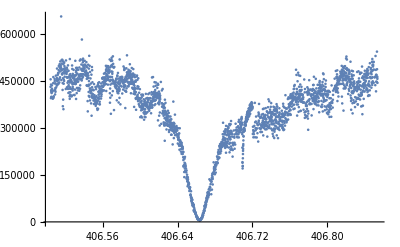

```mathematica
refspec=Import[names[[1]],"Table"];
xydata=Total[Partition[{refspec[[2;;,1]],refspec[[2;;,9]]}ᵀ,1]ᵀ/1];trimxy=xydata/."NaN"-> Sequence[];mask=Length[#]>1&/@trimxy;xyreal=Complement[trimxy*Boole[mask],{{0}}][[2;;]];
ListPlot[xyreal]
```

```mathematica
t[x_,x0_,g_,κ_,γ_,δ_,α_,ϕ_]:=(√κ)/(I (x-x0) + g^2/(I(x-x0+δ)+γ/2)+κ/2)+α*ⅇ^(ⅈ*ϕ);
```

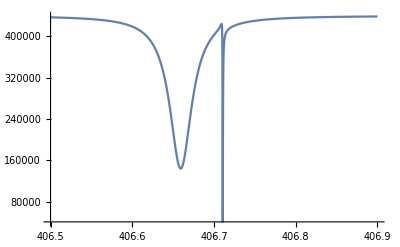

```mathematica
Plot[(8971*Abs[t[x,406.66,.006,.033,0.0001,-.05,-7,0]]^2),{x,406.5,406.9},PlotRange->All]
```

```mathematica
711-665
```

46

```mathematica
xyreal//Length
```

2398

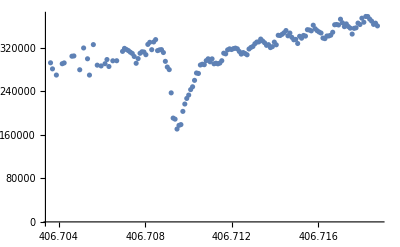

```mathematica
ListPlot[xyreal[[1350;;1500]]]
```

General::munfl: (8.84538×10^-38)^1195.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.9698×10^-30)^1195.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.65832×10^-43)^1195.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 406.66 | 2.47343×10^-18 | 1.64411×10^20 | 0.
g | 0.00212703 | 0.000180449 | 11.7874 | 3.25483×10^-31
κ | 0.033 | 1.64894×10^-18 | 2.00129×10^16 | 0.
B | 500000. | 6.18473×10^-18 | 8.08442×10^22 | 0.
δ | -0.0504094 | 0.0000182951 | -2755.35 | 0.
α | -7.00954 | 0.00742607 | -943.911 | 0.
ϕ | -0.112123 | 0.00221378 | -50.6479 | 0.

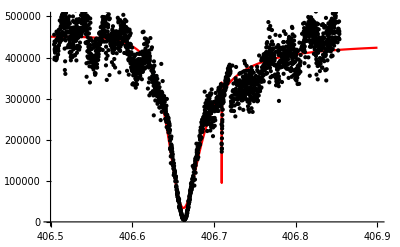

```mathematica
Cfit=NonlinearModelFit[xyreal,B(Abs[t[x,x0,g,κ,γ,δ,α,ϕ]])^2/.{γ-> 0.0001,κ-> .049,x0-> 406.659,B-> 8971},{{x0,406.66},{g,.01},{κ,0.033},{B,500000},{δ,-.049},{α,-10},{ϕ,0}},x];
Cfit["ParameterTable"]
Plot[Cfit[x],{x,406.5,406.9},Epilog->Point[xyreal],PlotStyle->Red,PlotRange->{0,500000}]
```

#### Bare cavity:

```mathematica
names=
Sort[Cases[FileNames[],_?((StringMatchQ[#,"*reflection1.txt"])&&!StringMatchQ[#,"*History*"]&)],FileDate[#1,"Modification"]<FileDate[#2,"Modification"]&];
Table[Print[i,": ",names[[i]]],{i,1,Length[names]}];
```

1: Cavity in reflection1.txt

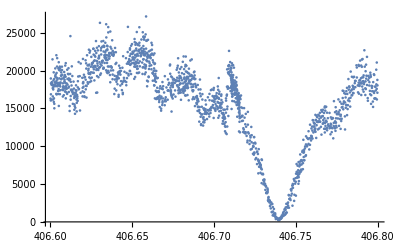

```mathematica
refspec=Import[names[[1]],"Table"];
xydata=Total[Partition[{refspec[[2;;,1]],refspec[[2;;,5]]}ᵀ,1]ᵀ/1];trimxy=xydata/."NaN"-> Sequence[];mask=Length[#]>1&/@trimxy;xyreal=Complement[trimxy*Boole[mask],{{0}}][[2;;]];
ListPlot[xyreal]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 1.00479 | 0.00428138 | 234.689 | 3.61258490292×10^-1240
B | -0.0508779 | 0.00090987 | -55.9178 | 2.02729241427×10^-378
X0 | 0.0000850777 | 0.000193113 | 0.440559 | 0.659592
κ | 0.0330766 | 0.000674198 | 49.0607 | 4.59397089434×10^-321

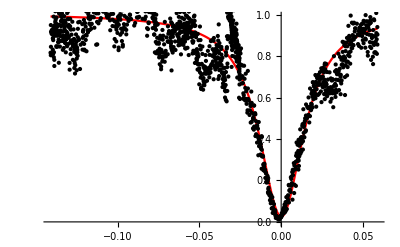

```mathematica
Lorentz[bg_,amp_,x0_,Γ_,x_]:=bg+amp*PDF[CauchyDistribution[x0,Γ],x];
Cnorm={xyreal[[All,1]]-406.741,xyreal[[All,2]]/Mean[xyreal[[1;;500,2]]]}ᵀ;
Cfit=NonlinearModelFit[Cnorm,Lorentz[A,B,X0,κ/2,x],{{A,2000},{B,-1300},{X0,0},{κ,.04}},x];
Cfit["ParameterTable"]
Plot[Cfit[x],{x,Cfit["Data"][[1,1]],Cfit["Data"][[-1,1]]},Epilog->Point[Cfit["Data"]],PlotStyle->Red]
```

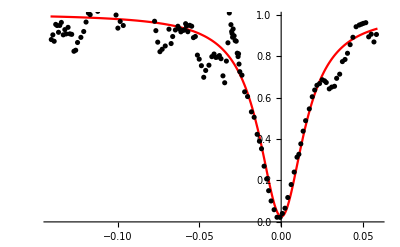

```mathematica
binby=10;
xybin=Total[Partition[Cnorm,binby]ᵀ/binby];
Show[{Plot[Cfit[x],{x,Cfit["Data"][[1,1]],Cfit["Data"][[-1,1]]},PlotStyle->Red],ListPlot[xybin,PlotStyle->Black]}]
```

#### SiV on resonance

```mathematica
SetDirectory[NotebookDirectory[]];
names=
Sort[Cases[FileNames[],_?((StringMatchQ[#,"*PLE*image.txt"])&&!StringMatchQ[#,"*History*"]&)],FileDate[#1,"Modification"]<FileDate[#2,"Modification"]&];
Table[Print[i,": ",names[[i]]],{i,1,Length[names]}];
```

1: 14.45.08_Pulse Experiment_Two laser PLE_ID8_image.txt

2: 13.20.05_Pulse Experiment_SiV PLE  on resonance_ID1_image.txt

3: 10.50.18_Pulse Experiment_1laser PLE  1Mcts , NO green_ID5_image.txt

4: 15.27.58_Pulse Experiment_PLE SiV dn_ID7_image.txt

5: 15.29.50_Pulse Experiment_PLE SiV up_ID8_image.txt

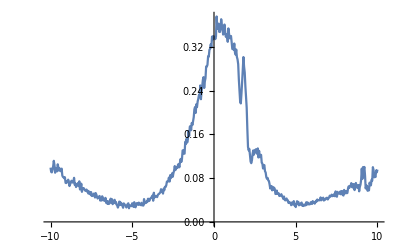

```mathematica
data=Import[#,"Table"]&/@names;
XYdata=Total[Partition[{data[[2,All,1]],data[[2,All,2]]}ᵀ,1]ᵀ/1];
ListLinePlot[XYdata]
```

```mathematica
t[x_,x0_,g_,κ_,γ_,δ_,α_,ϕ_]:=(√κ)/(I (x-x0-δ) + g^2/(I(x-x0)+γ/2)+κ/2)+α E^(ⅈ ϕ);
Rnorm={XYdata[[All,1]]/1000,XYdata[[All,2]]/Max[XYdata[[All,2]]]}ᵀ;
```

General::munfl: 0.0150195^247.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0075696^247.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0027552^247.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 0.000516202 | 0.0000176889 | 29.1822 | 1.20648×10^-109
B | 0.0144588 | 0.0000802496 | 180.172 | 0.
δ | 0. | 1.30115×10^-17 | 0. | 1.
g | 0.00528071 | 0.0000207289 | 254.751 | 0.
α | -8.48325 | 0.0200417 | -423.279 | 0.
ϕ | 12.5899 | 0.00354635 | 3550.1 | 0.

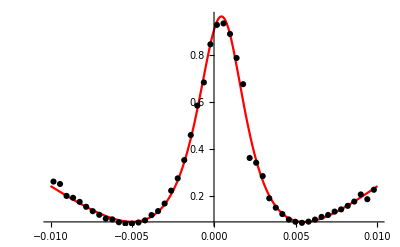

```mathematica
Rfit=NonlinearModelFit[Rnorm,A+B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.{A-> 0,κ-> .0331,γ-> 0.0001,δ-> 0},{{x0,0},{B,1.55},{δ,0},{g, .006},{α,-.5},{ϕ,12}},x];
Rfit["ParameterTable"]
binby=10;
Rxybin=Total[Partition[Rnorm,binby]ᵀ/binby];
Show[{Plot[Rfit[x],{x,-.01,.01},PlotStyle->Red],ListPlot[Rxybin,PlotStyle->Black]}]
```

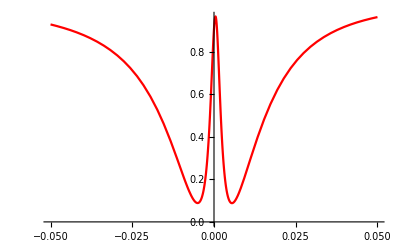

```mathematica
Plot[{Cfit[x],Rfit[x]},{x,-.05,.05},PlotStyle->{Directive[Black,Dashed],Red}]
```

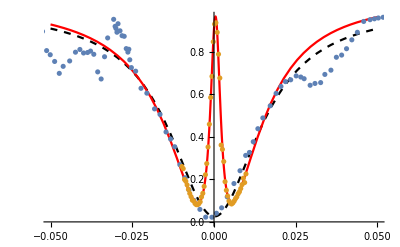

```mathematica
Show[{Plot[{Cfit[x],Rfit[x]},{x,-.05,.05},PlotStyle->{Directive[Black,Dashed],Red},AxesOrigin-> -.05],ListPlot[{xybin,Rxybin}]}]
```

```mathematica
(4*5.6^2)/(33*0.1)
```

38.0121

#### Cavity half-detuned

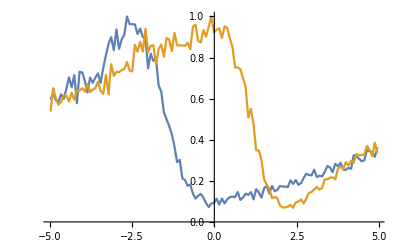

```mathematica
rawdn=Total[Partition[{data[[4,All,1]],data[[4,All,2]]}ᵀ,4]ᵀ/4];
rawup=Total[Partition[{data[[5,All,1]],data[[5,All,2]]}ᵀ,4]ᵀ/4];
XYdatadn={rawdn[[All,1]],rawdn[[All,2]]/Max[rawdn[[All,2]]]}ᵀ;
XYdataup={rawup[[All,1]],rawup[[All,2]]/Max[rawup[[All,2]]]}ᵀ;
ListLinePlot[{XYdatadn,XYdataup}]
```

| Estimate | Standard Error | t-Statistic | P-Value
x0 | -2.61589 | 0.0409039 | -63.952 | 1.45348×10^-94
B | 14.3136 | 0.344273 | 41.5765 | 4.1308×10^-73
δ | -8.56955 | 0.482187 | -17.7723 | 2.09174×10^-35
α | -0.26693 | 0.00281432 | -94.8471 | 1.06408×10^-114
ϕ | -0.0636794 | 0.0196073 | -3.24775 | 0.00150864

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 2.03911 | 0.0447617 | 45.5549 | 1.36555×10^-77
B | 4.95673 | 0.279623 | 17.7264 | 2.61945×10^-35
δ | 7.77476 | 0.505976 | 15.3659 | 4.02442×10^-30
α | -0.115794 | 0.0162722 | -7.11607 | 8.77885×10^-11
ϕ | 2.39099 | 0.103256 | 23.1559 | 4.29977×10^-46

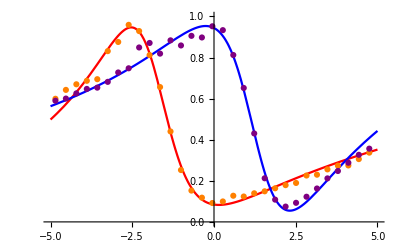

```mathematica
Dfit=NonlinearModelFit[XYdatadn,A+B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.{A-> 0,g-> 5.27,κ-> 33.1,γ-> 0.1},{{x0,-1.5},{B,-10},{δ,16},{α,-.45},{ϕ,0.06}},x];
Ufit=NonlinearModelFit[XYdataup,A+B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.{A-> 0,g-> 5.27,κ-> 33.1,γ-> 0.1},{{x0,1.5},{B,-10},{δ,16},{α,0},{ϕ,0}},x];
Dfit["ParameterTable"]
Ufit["ParameterTable"]
binby=4;
Dxybin=Total[Partition[XYdatadn,binby]ᵀ/binby];
Uxybin=Total[Partition[XYdataup,binby]ᵀ/binby];
Show[{Plot[{Dfit[x],Ufit[x]},{x,-5,5},PlotStyle->{Red,Blue},PlotRange->{0,1}],ListPlot[{Dxybin,Uxybin},PlotStyle->{Orange,Purple}]}]
```

```mathematica
8/33.
```

0.242424

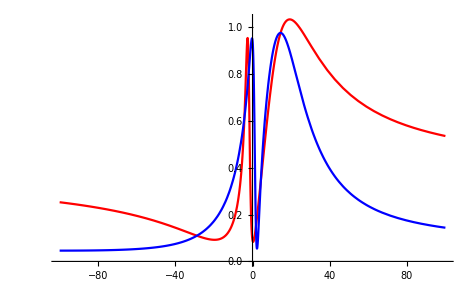

```mathematica
Plot[{Dfit[x],Ufit[x]},{x,-100,100},PlotStyle->{Red,Blue}]
```

#### Few kappa detuned

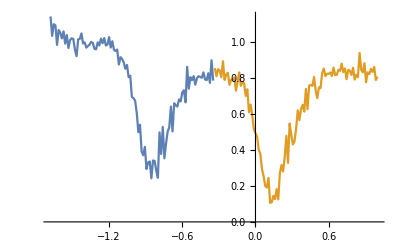

```mathematica
XYdataS=Total[Partition[{data[[3,All,1]],(2*data[[3,All,2]]-Mean[data[[3,All,2]]])/(Max[data[[3,All,2]]])}ᵀ,1]ᵀ/1];
ListLinePlot[{XYdataS[[100;;200]],XYdataS[[201;;]]},AxesOrigin->0]
```

```mathematica
XYdataSup=XYdataS[[100;;200]];
XYdataSdn=XYdataS[[201;;]];
```

| Estimate | Standard Error | t-Statistic | P-Value
x0 | -0.27136 | 0.0134511 | -20.1738 | 2.68569×10^-36
B | 31.3319 | 0.826847 | 37.8932 | 1.51855×10^-59
δ | -65.0315 | 2.16428 | -30.0477 | 1.27022×10^-50
α | -0.173989 | 0.00271171 | -64.1622 | 1.21402×10^-80
ϕ | -0.0545858 | 0.0103793 | -5.2591 | 8.76926×10^-7

| Estimate | Standard Error | t-Statistic | P-Value
x0 | -0.478703 | 0.0147332 | -32.4915 | 1.3582×10^-53
B | 4.03096 | 0.344412 | 11.7039 | 3.46371×10^-20
δ | 62.8984 | 2.09845 | 29.9737 | 1.57349×10^-50
α | -0.450717 | 0.0201714 | -22.3443 | 8.12533×10^-40
ϕ | 5.59055 | 0.0358113 | 156.111 | 2.55772×10^-117

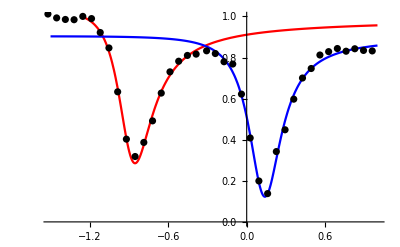

```mathematica
SDfit=NonlinearModelFit[XYdataSdn,A+B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.{A-> 0,g-> 5.27,κ-> 33.1,γ-> 0.1},{{x0,0.1},{B,-10},{δ,60},{α,0},{ϕ,0}},x];
SUfit=NonlinearModelFit[XYdataSup,A+B*Abs[t[x,x0,g,κ,γ,δ,α,ϕ]]^2/.{A-> 0,g-> 5.27,κ-> 33.1,γ-> 0.1},{{x0,-0.8},{B,-10},{δ,62},{α,0},{ϕ,0}},x];
SDfit["ParameterTable"]
SUfit["ParameterTable"]
binby=5;
SDxybin=Total[Partition[XYdataSdn,binby]ᵀ/binby];
SUxybin=Total[Partition[XYdataSup,binby]ᵀ/binby];
Show[{Plot[{SUfit[x],SDfit[x]},{x,-1.5,1},PlotStyle->{Red,Blue},PlotRange->{0,1}],ListPlot[{SDxybin,SUxybin},PlotStyle->Black]}]
```

```mathematica
34*1/(1+4*(0.25)^2)
```

27.2

Expected transmission dip:  T~1/(1+C)^2

```mathematica
1-1./(1+34)^2
```

0.999184